```mathematica
Import Data
```

```mathematica
SetDirectory["/Users/Chris/Documents/Coronavirus/HE_Distributions/PairwiseCode/Simulations"];
weights=Import["Weightings.dat","Table"][[2;;]];
```

```mathematica
CDF[LogNormalDistribution[1.434065,0.6612],0.5]
```

0.000647243

```mathematica
Direct transmission
```

```mathematica
(*Within-host evolution per day*)
gg=0.0655;
(*Sequencing error*)
e=0.207;
sims=ConstantArray[0,100000];
Monitor[For[i=1,i<=100000,i++,
(*Time to symptom onset in A*)
sa=0;
While[sa==0,
sa=Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];
];
(*Time to causing infection in B*)
tab=sa+Floor[RandomVariate[GammaDistribution[weights[[sa,2]],weights[[sa,3]]]]-weights[[sa,1]]+0.5];
(*Time to symptom onset in B*)
sb=tab+Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];
(*Time to collecting sequence from A*)
da=sa+Floor[RandomVariate[UniformDistribution[{2,10}]]+0.5];
(*Time to collecting sequence from B*)
db=sb+Floor[RandomVariate[UniformDistribution[{2,10}]]+0.5];
If[da>=tab,
evotimea=da-tab;
evotimeb=db-tab;
];
If[da<tab,
evotimea=0;
evotimeb=db-da;
];
eva=RandomVariate[PoissonDistribution[gg*evotimea+e]];
evb=RandomVariate[PoissonDistribution[gg*evotimeb+e]];
sims[[i]]={sa,sb,da,db,eva,evb};
],i];
```

```mathematica
Export["/Users/Chris/Documents/Coronavirus/HE_Distributions/PairwiseCode/Simulations/Direct.dat",sims];
```

```mathematica
Indirect A to C to B transmission
```

```mathematica
(*Within-host evolution per day*)
gg=0.0655;
(*Sequencing error*)
e=0.207;
sims=ConstantArray[0,100000];
Monitor[For[i=1,i<=100000,i++,
(*Time to symptom onset in A*)
While[sa==0||sa>=80,
sa=Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];
];
(*Time to causing infection in C*)
tac=sa+Floor[RandomVariate[GammaDistribution[weights[[sa,2]],weights[[sa,3]]]]-weights[[sa,1]]+0.5];
(*Time to symptom onset in C*)
sc=tac;
While[sc==tac,
sc=tac+Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];
];
(*Time to causing infection in B*)
tcb=sc+Floor[RandomVariate[GammaDistribution[weights[[(sc-tac),2]],weights[[(sc-tac),3]]]]-weights[[(sc-tac),1]]+0.5];
(*Time to symptom onset in B*)
sb=tcb+Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];
(*Time to collecting sequence from A*)
da=sa+Floor[RandomVariate[UniformDistribution[{2,10}]]+0.5];
(*Time to collecting sequence from B*)
db=sb+Floor[RandomVariate[UniformDistribution[{2,10}]]+0.5];
If[da>=tab,
evotimea=da-tab;
evotimeb=db-tab;
];
If[da<tab,
evotimea=0;
evotimeb=db-da;
];
eva=RandomVariate[PoissonDistribution[gg*evotimea+e]];
evb=RandomVariate[PoissonDistribution[gg*evotimeb+e]];
sims[[i]]={sa,sb,da,db,eva,evb};
],i];
```

```mathematica
Export["/Users/Chris/Documents/Coronavirus/HE_Distributions/PairwiseCode/Simulations/Indirect1.dat",sims];
```

```mathematica
Indirect A to C to D to B
```

```mathematica
(*Within-host evolution per day*)
gg=0.0655;
(*Sequencing error*)
e=0.207;
sims=ConstantArray[0,100000];
Monitor[For[i=1,i<=100000,i++,
(*Time to symptom onset in A*)
While[sa==0||sa>=80,
sa=Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];
];
(*Time to causing infection in C*)
tac=sa+Floor[RandomVariate[GammaDistribution[weights[[sa,2]],weights[[sa,3]]]]-weights[[sa,1]]+0.5];
(*Time to symptom onset in C*)
sc=tac;
While[sc==tac||sc>=tac+80,
sc=tac+Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];
];
(*Time to causing infection in D*)
tcd=sc+Floor[RandomVariate[GammaDistribution[weights[[(sc-tac),2]],weights[[(sc-tac),3]]]]-weights[[(sc-tac),1]]+0.5];
(*Time to symptom onset in D*)
sd=tcd;
While[sd==tcd||sd>=tcd+80,
sd=tcd+Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];
];
(*Time to causing infection in B*)
tdb=sd+Floor[RandomVariate[GammaDistribution[weights[[(sd-tcd),2]],weights[[(sd-tcd),3]]]]-weights[[(sd-tcd),1]]+0.5];
(*Time to symptom onset in D*)
sb=tdb+Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];
(*Time to collecting sequence from A*)
da=sa+Floor[RandomVariate[UniformDistribution[{2,10}]]+0.5];
(*Time to collecting sequence from B*)
db=sb+Floor[RandomVariate[UniformDistribution[{2,10}]]+0.5];
If[da>=tab,
evotimea=da-tab;
evotimeb=db-tab;
];
If[da<tab,
evotimea=0;
evotimeb=db-da;
];
eva=RandomVariate[PoissonDistribution[gg*evotimea+e]];
evb=RandomVariate[PoissonDistribution[gg*evotimeb+e]];
sims[[i]]={sa,sb,da,db,eva,evb};
],i];
```

```mathematica
Export["/Users/Chris/Documents/Coronavirus/HE_Distributions/PairwiseCode/Simulations/Indirect2.dat",sims];
```

```mathematica
Indirect A to C to D to E to B
```

```mathematica
(*Within-host evolution per day*)
gg=0.0655;
(*Sequencing error*)
e=0.207;
sims=ConstantArray[0,100000];
Monitor[For[i=1,i<=100000,i++,
(*Time to symptom onset in A*)
While[sa==0,
sa=Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];
];
(*Time to causing infection in C*)
tac=sa+Floor[RandomVariate[GammaDistribution[weights[[sa,2]],weights[[sa,3]]]]-weights[[sa,1]]+0.5];
(*Time to symptom onset in C*)
sc=tac;
While[sc==tac||sc>=tac+80,
sc=tac+Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];
];
(*Time to causing infection in D*)
tcd=sc+Floor[RandomVariate[GammaDistribution[weights[[(sc-tac),2]],weights[[(sc-tac),3]]]]-weights[[(sc-tac),1]]+0.5];
(*Time to symptom onset in D*)
sd=tcd;
While[sd==tcd||sd>=tcd+80,
sd=tcd+Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];
];
(*Time to causing infection in E*)
tde=sd+Floor[RandomVariate[GammaDistribution[weights[[(sd-tcd),2]],weights[[(sd-tcd),3]]]]-weights[[(sd-tcd),1]]+0.5];
(*Time to symptom onset in E*)
se=tde;
While[se==tde||se>=tde+80,
se=tde+Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];
];
(*Time to causing infection in B*)
teb=se+Floor[RandomVariate[GammaDistribution[weights[[(se-tde),2]],weights[[(se-tde),3]]]]-weights[[(se-tde),1]]+0.5];
(*Time to symptom onset in B*)
sb=teb+Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];
(*Time to collecting sequence from A*)
da=sa+Floor[RandomVariate[UniformDistribution[{2,10}]]+0.5];
(*Time to collecting sequence from B*)
db=sb+Floor[RandomVariate[UniformDistribution[{2,10}]]+0.5];
If[da>=tab,
evotimea=da-tab;
evotimeb=db-tab;
];
If[da<tab,
evotimea=0;
evotimeb=db-da;
];
eva=RandomVariate[PoissonDistribution[gg*evotimea+e]];
evb=RandomVariate[PoissonDistribution[gg*evotimeb+e]];
sims[[i]]={sa,sb,da,db,eva,evb};
],i];
```

```mathematica
Export["/Users/Chris/Documents/Coronavirus/HE_Distributions/PairwiseCode/Simulations/Indirect3.dat",sims];
```

```mathematica
Indirect A to CDEF to B
```

```mathematica
(*Within-host evolution per day*)
gg=0.0655;
(*Sequencing error*)
e=0.207;
evotimea=0;
evotimeb=0;
sims=ConstantArray[0,100000];
Monitor[For[i=1,i<=100000,i++,
(*Time to symptom onset in A*)
sa=0;
While[sa==0||sa>=80,
sa=Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];
];
(*Time to causing infection in C*)
tac=sa+Floor[RandomVariate[GammaDistribution[weights[[sa,2]],weights[[sa,3]]]]-weights[[sa,1]]+0.5];
(*Time to symptom onset in C*)
sc=tac;
While[sc==tac||sc>=tac+80,
sc=tac+Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];
];
(*Time to causing infection in D*)
tcd=sc+Floor[RandomVariate[GammaDistribution[weights[[(sc-tac),2]],weights[[(sc-tac),3]]]]-weights[[(sc-tac),1]]+0.5];
(*Time to symptom onset in D*)
sd=tcd;
While[sd==tcd||sd>=tcd+80,
sd=tcd+Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];
];
(*Time to causing infection in E*)
tde=sd+Floor[RandomVariate[GammaDistribution[weights[[(sd-tcd),2]],weights[[(sd-tcd),3]]]]-weights[[(sd-tcd),1]]+0.5];
(*Time to symptom onset in E*)
se=tde;
While[se==tde||se>=tde+80,
se=tde+Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];
];

(*Time to causing infection in F*)
tef=se+Floor[RandomVariate[GammaDistribution[weights[[(se-tde),2]],weights[[(se-tde),3]]]]-weights[[(se-tde),1]]+0.5];
(*Time to symptom onset in F*)
sf=tef;
While[sf==tef||sf>=tef+80,
sf=tef+Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];
];

(*Time to causing infection in B*)
tfb=sf+Floor[RandomVariate[GammaDistribution[weights[[(sf-tef),2]],weights[[(sf-tef),3]]]]-weights[[(sf-tef),1]]+0.5];
(*Time to symptom onset in B*)
sb=tfb+Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];

(*Time to collecting sequence from A*)
da=sa+Floor[RandomVariate[UniformDistribution[{2,10}]]+0.5];
(*Time to collecting sequence from B*)
db=sb+Floor[RandomVariate[UniformDistribution[{2,10}]]+0.5];
If[da>=tab,
evotimea=da-tab;
evotimeb=db-tab;
];
If[da<tab,
evotimea=0;
evotimeb=db-da;
];
eva=RandomVariate[PoissonDistribution[gg*evotimea+e]];
evb=RandomVariate[PoissonDistribution[gg*evotimeb+e]];
sims[[i]]={sa,sb,da,db,eva,evb};
],i];
```

```mathematica
Export["/Users/Chris/Documents/Coronavirus/HE_Distributions/PairwiseCode/Simulations/Indirect4.dat",sims];
```

```mathematica
Indirect A to CDEFG to B
```

```mathematica
(*Within-host evolution per day*)
gg=0.0655;
(*Sequencing error*)
e=0.207;
evotimea=0;
evotimeb=0;
sims=ConstantArray[0,100000];
Monitor[For[i=1,i<=100000,i++,
(*Time to symptom onset in A*)
sa=0;
While[sa==0||sa>=80,
sa=Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];
];
(*Time to causing infection in C*)
tac=sa+Floor[RandomVariate[GammaDistribution[weights[[sa,2]],weights[[sa,3]]]]-weights[[sa,1]]+0.5];
(*Time to symptom onset in C*)
sc=tac;
While[sc==tac||sc>=tac+80,
sc=tac+Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];
];
(*Time to causing infection in D*)
tcd=sc+Floor[RandomVariate[GammaDistribution[weights[[(sc-tac),2]],weights[[(sc-tac),3]]]]-weights[[(sc-tac),1]]+0.5];
(*Time to symptom onset in D*)
sd=tcd;
While[sd==tcd||sd>=tcd+80,
sd=tcd+Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];
];
(*Time to causing infection in E*)
tde=sd+Floor[RandomVariate[GammaDistribution[weights[[(sd-tcd),2]],weights[[(sd-tcd),3]]]]-weights[[(sd-tcd),1]]+0.5];
(*Time to symptom onset in E*)
se=tde;
While[se==tde||se>=tde+80,
se=tde+Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];
];
(*Time to causing infection in F*)
tef=se+Floor[RandomVariate[GammaDistribution[weights[[(se-tde),2]],weights[[(se-tde),3]]]]-weights[[(se-tde),1]]+0.5];
(*Time to symptom onset in F*)
sf=tef;
While[sf==tef||sf>=tef+80,
sf=tef+Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];
];

(*Time to causing infection in G*)
tfg=sf+Floor[RandomVariate[GammaDistribution[weights[[(sf-tef),2]],weights[[(sf-tef),3]]]]-weights[[(sf-tef),1]]+0.5];
(*Time to symptom onset in G*)
sg=tfg;
While[sg==tfg||sg>=tfg+80,
sg=tfg+Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];
];

(*Time to causing infection in B*)
tgb=sg+Floor[RandomVariate[GammaDistribution[weights[[(sg-tfg),2]],weights[[(sg-tfg),3]]]]-weights[[(sg-tfg),1]]+0.5];
(*Time to symptom onset in B*)
sb=tgb+Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];

(*Time to collecting sequence from A*)
da=sa+Floor[RandomVariate[UniformDistribution[{2,10}]]+0.5];
(*Time to collecting sequence from B*)
db=sb+Floor[RandomVariate[UniformDistribution[{2,10}]]+0.5];
If[da>=tab,
evotimea=da-tab;
evotimeb=db-tab;
];
If[da<tab,
evotimea=0;
evotimeb=db-da;
];
eva=RandomVariate[PoissonDistribution[gg*evotimea+e]];
evb=RandomVariate[PoissonDistribution[gg*evotimeb+e]];
sims[[i]]={sa,sb,da,db,eva,evb};
],i];
```

```mathematica
Export["/Users/Chris/Documents/Coronavirus/HE_Distributions/PairwiseCode/Simulations/Indirect5.dat",sims];
```

```mathematica
Indirect A to CDEFGH to B
```

```mathematica
(*Within-host evolution per day*)
gg=0.0655;
(*Sequencing error*)
e=0.207;
evotimea=0;
evotimeb=0;
sims=ConstantArray[0,100000];
Monitor[For[i=1,i<=100000,i++,
(*Time to symptom onset in A*)
sa=0;
While[sa==0||sa>=80,
sa=Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];
];
(*Time to causing infection in C*)
tac=sa+Floor[RandomVariate[GammaDistribution[weights[[sa,2]],weights[[sa,3]]]]-weights[[sa,1]]+0.5];
(*Time to symptom onset in C*)
sc=tac;
While[sc==tac||sc>=tac+80,
sc=tac+Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];
];
(*Time to causing infection in D*)
tcd=sc+Floor[RandomVariate[GammaDistribution[weights[[(sc-tac),2]],weights[[(sc-tac),3]]]]-weights[[(sc-tac),1]]+0.5];
(*Time to symptom onset in D*)
sd=tcd;
While[sd==tcd||sd>=tcd+80,
sd=tcd+Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];
];
(*Time to causing infection in E*)
tde=sd+Floor[RandomVariate[GammaDistribution[weights[[(sd-tcd),2]],weights[[(sd-tcd),3]]]]-weights[[(sd-tcd),1]]+0.5];
(*Time to symptom onset in E*)
se=tde;
While[se==tde||se>=tde+80,
se=tde+Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];
];
(*Time to causing infection in F*)
tef=se+Floor[RandomVariate[GammaDistribution[weights[[(se-tde),2]],weights[[(se-tde),3]]]]-weights[[(se-tde),1]]+0.5];
(*Time to symptom onset in F*)
sf=tef;
While[sf==tef||sf>=tef+80,
sf=tef+Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];
];
(*Time to causing infection in G*)
tfg=sf+Floor[RandomVariate[GammaDistribution[weights[[(sf-tef),2]],weights[[(sf-tef),3]]]]-weights[[(sf-tef),1]]+0.5];
(*Time to symptom onset in G*)
sg=tfg;
While[sg==tfg||sg>=tfg+80,
sg=tfg+Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];
];
(*Time to causing infection in H*)
tgh=sg+Floor[RandomVariate[GammaDistribution[weights[[(sg-tfg),2]],weights[[(sg-tfg),3]]]]-weights[[(sg-tfg),1]]+0.5];
(*Time to symptom onset in H*)
sh=tgh;
While[sh==tgh||sh>=tgh+80,
sh=tgh+Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];
];

(*Time to causing infection in B*)
thb=sh+Floor[RandomVariate[GammaDistribution[weights[[(sh-tgh),2]],weights[[(sh-tgh),3]]]]-weights[[(sh-tgh),1]]+0.5];
(*Time to symptom onset in B*)
sb=thb+Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];

(*Time to collecting sequence from A*)
da=sa+Floor[RandomVariate[UniformDistribution[{2,10}]]+0.5];
(*Time to collecting sequence from B*)
db=sb+Floor[RandomVariate[UniformDistribution[{2,10}]]+0.5];
If[da>=tab,
evotimea=da-tab;
evotimeb=db-tab;
];
If[da<tab,
evotimea=0;
evotimeb=db-da;
];
eva=RandomVariate[PoissonDistribution[gg*evotimea+e]];
evb=RandomVariate[PoissonDistribution[gg*evotimeb+e]];
sims[[i]]={sa,sb,da,db,eva,evb};
],i];
```

```mathematica
Export["/Users/Chris/Documents/Coronavirus/HE_Distributions/PairwiseCode/Simulations/Indirect6.dat",sims];
```

```mathematica
Indirect A to CDEFGHI to B
```

```mathematica
(*Within-host evolution per day*)
gg=0.0655;
(*Sequencing error*)
e=0.207;
evotimea=0;
evotimeb=0;
sims=ConstantArray[0,100000];
Monitor[For[i=1,i<=100000,i++,
(*Time to symptom onset in A*)
sa=0;
While[sa==0||sa>=80,
sa=Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];
];
(*Time to causing infection in C*)
tac=sa+Floor[RandomVariate[GammaDistribution[weights[[sa,2]],weights[[sa,3]]]]-weights[[sa,1]]+0.5];
(*Time to symptom onset in C*)
sc=tac;
While[sc==tac||sc>=tac+80,
sc=tac+Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];
];
(*Time to causing infection in D*)
tcd=sc+Floor[RandomVariate[GammaDistribution[weights[[(sc-tac),2]],weights[[(sc-tac),3]]]]-weights[[(sc-tac),1]]+0.5];
(*Time to symptom onset in D*)
sd=tcd;
While[sd==tcd||sd>=tcd+80,
sd=tcd+Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];
];
(*Time to causing infection in E*)
tde=sd+Floor[RandomVariate[GammaDistribution[weights[[(sd-tcd),2]],weights[[(sd-tcd),3]]]]-weights[[(sd-tcd),1]]+0.5];
(*Time to symptom onset in E*)
se=tde;
While[se==tde||se>=tde+80,
se=tde+Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];
];
(*Time to causing infection in F*)
tef=se+Floor[RandomVariate[GammaDistribution[weights[[(se-tde),2]],weights[[(se-tde),3]]]]-weights[[(se-tde),1]]+0.5];
(*Time to symptom onset in F*)
sf=tef;
While[sf==tef||sf>=tef+80,
sf=tef+Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];
];
(*Time to causing infection in G*)
tfg=sf+Floor[RandomVariate[GammaDistribution[weights[[(sf-tef),2]],weights[[(sf-tef),3]]]]-weights[[(sf-tef),1]]+0.5];
(*Time to symptom onset in G*)
sg=tfg;
While[sg==tfg||sg>=tfg+80,
sg=tfg+Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];
];
(*Time to causing infection in H*)
tgh=sg+Floor[RandomVariate[GammaDistribution[weights[[(sg-tfg),2]],weights[[(sg-tfg),3]]]]-weights[[(sg-tfg),1]]+0.5];
(*Time to symptom onset in H*)
sh=tgh;
While[sh==tgh||sh>=tgh+80,
sh=tgh+Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];
];
(*Time to causing infection in I*)
thi=sh+Floor[RandomVariate[GammaDistribution[weights[[(sh-tgh),2]],weights[[(sh-tgh),3]]]]-weights[[(sh-tgh),1]]+0.5];
(*Time to symptom onset in I*)
si=thi;
While[si==thi||si>=thi+80,
si=thi+Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];
];

(*Time to causing infection in B*)
tib=si+Floor[RandomVariate[GammaDistribution[weights[[(si-thi),2]],weights[[(si-thi),3]]]]-weights[[(si-thi),1]]+0.5];
(*Time to symptom onset in B*)
sb=tib+Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];

(*Time to collecting sequence from A*)
da=sa+Floor[RandomVariate[UniformDistribution[{2,10}]]+0.5];
(*Time to collecting sequence from B*)
db=sb+Floor[RandomVariate[UniformDistribution[{2,10}]]+0.5];
If[da>=tab,
evotimea=da-tab;
evotimeb=db-tab;
];
If[da<tab,
evotimea=0;
evotimeb=db-da;
];
eva=RandomVariate[PoissonDistribution[gg*evotimea+e]];
evb=RandomVariate[PoissonDistribution[gg*evotimeb+e]];
sims[[i]]={sa,sb,da,db,eva,evb};
],i];
```

```mathematica
Export["/Users/Chris/Documents/Coronavirus/HE_Distributions/PairwiseCode/Simulations/Indirect7.dat",sims];
```

```mathematica
Indirect A to CDEFGHIJ to B
```

```mathematica
(*Within-host evolution per day*)
gg=0.0655;
(*Sequencing error*)
e=0.207;
evotimea=0;
evotimeb=0;
sims=ConstantArray[0,100000];
Monitor[For[i=1,i<=100000,i++,
(*Time to symptom onset in A*)
sa=0;
While[sa==0||sa>=80,
sa=Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];
];
(*Time to causing infection in C*)
tac=sa+Floor[RandomVariate[GammaDistribution[weights[[sa,2]],weights[[sa,3]]]]-weights[[sa,1]]+0.5];
(*Time to symptom onset in C*)
sc=tac;
While[sc==tac||sc>=tac+80,
sc=tac+Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];
];
(*Time to causing infection in D*)
tcd=sc+Floor[RandomVariate[GammaDistribution[weights[[(sc-tac),2]],weights[[(sc-tac),3]]]]-weights[[(sc-tac),1]]+0.5];
(*Time to symptom onset in D*)
sd=tcd;
While[sd==tcd||sd>=tcd+80,
sd=tcd+Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];
];
(*Time to causing infection in E*)
tde=sd+Floor[RandomVariate[GammaDistribution[weights[[(sd-tcd),2]],weights[[(sd-tcd),3]]]]-weights[[(sd-tcd),1]]+0.5];
(*Time to symptom onset in E*)
se=tde;
While[se==tde||se>=tde+80,
se=tde+Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];
];
(*Time to causing infection in F*)
tef=se+Floor[RandomVariate[GammaDistribution[weights[[(se-tde),2]],weights[[(se-tde),3]]]]-weights[[(se-tde),1]]+0.5];
(*Time to symptom onset in F*)
sf=tef;
While[sf==tef||sf>=tef+80,
sf=tef+Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];
];
(*Time to causing infection in G*)
tfg=sf+Floor[RandomVariate[GammaDistribution[weights[[(sf-tef),2]],weights[[(sf-tef),3]]]]-weights[[(sf-tef),1]]+0.5];
(*Time to symptom onset in G*)
sg=tfg;
While[sg==tfg||sg>=tfg+80,
sg=tfg+Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];
];
(*Time to causing infection in H*)
tgh=sg+Floor[RandomVariate[GammaDistribution[weights[[(sg-tfg),2]],weights[[(sg-tfg),3]]]]-weights[[(sg-tfg),1]]+0.5];
(*Time to symptom onset in H*)
sh=tgh;
While[sh==tgh||sh>=tgh+80,
sh=tgh+Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];
];
(*Time to causing infection in I*)
thi=sh+Floor[RandomVariate[GammaDistribution[weights[[(sh-tgh),2]],weights[[(sh-tgh),3]]]]-weights[[(sh-tgh),1]]+0.5];
(*Time to symptom onset in I*)
si=thi;
While[si==thi||si>=thi+80,
si=thi+Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];
];

(*Time to causing infection in J*)
tij=si+Floor[RandomVariate[GammaDistribution[weights[[(si-thi),2]],weights[[(si-thi),3]]]]-weights[[(si-thi),1]]+0.5];
(*Time to symptom onset in J*)
sj=tij;
While[sj==tij||sj>=tij+80,
sj=tij+Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];
];

(*Time to causing infection in B*)
tjb=sj+Floor[RandomVariate[GammaDistribution[weights[[(sj-tij),2]],weights[[(sj-tij),3]]]]-weights[[(sj-tij),1]]+0.5];
(*Time to symptom onset in B*)
sb=tjb+Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];

(*Time to collecting sequence from A*)
da=sa+Floor[RandomVariate[UniformDistribution[{2,10}]]+0.5];
(*Time to collecting sequence from B*)
db=sb+Floor[RandomVariate[UniformDistribution[{2,10}]]+0.5];
If[da>=tab,
evotimea=da-tab;
evotimeb=db-tab;
];
If[da<tab,
evotimea=0;
evotimeb=db-da;
];
eva=RandomVariate[PoissonDistribution[gg*evotimea+e]];
evb=RandomVariate[PoissonDistribution[gg*evotimeb+e]];
sims[[i]]={sa,sb,da,db,eva,evb};
],i];
```

```mathematica
Export["/Users/Chris/Documents/Coronavirus/HE_Distributions/PairwiseCode/Simulations/Indirect8.dat",sims];
```

```mathematica
Indirect C to A and B
```

```mathematica
(*Within-host evolution per day*)
gg=0.0655;
(*Sequencing error*)
e=0.207;
sims=ConstantArray[0,100000];
Monitor[For[i=1,i<=100000,i++,
(*Time to symptom onset in A*)
While[sc==0,
sc=Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];
];
(*Time to causing infection in B*)
t1=sc+Floor[RandomVariate[GammaDistribution[weights[[sc,2]],weights[[sc,3]]]]-weights[[sc,1]]+0.5];
t2=sc+Floor[RandomVariate[GammaDistribution[weights[[sc,2]],weights[[sc,3]]]]-weights[[sc,1]]+0.5];
tca=Min[t1,t2];
tcb=Max[t1,t2];
(*Time to symptom onset in A*)
sa=tca+Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];
(*Time to symptom onset in B*)
sb=tcb+Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];
(*Time to collecting sequence from A*)
da=sa+Floor[RandomVariate[UniformDistribution[{2,10}]]+0.5];
(*Time to collecting sequence from B*)
db=sb+Floor[RandomVariate[UniformDistribution[{2,10}]]+0.5];
(*Evolutionary times: Transmission to A comes first*)
evotimea=da-tca;
evotimeb=db-tca;
eva=RandomVariate[PoissonDistribution[gg*evotimea+e]];
evb=RandomVariate[PoissonDistribution[gg*evotimeb+e]];
sims[[i]]={sa,sb,da,db,eva,evb};
],i];
```

```mathematica
Export["/Users/Chris/Documents/Coronavirus/HE_Distributions/PairwiseCode/Simulations/IndirectC_AB.dat",sims];
```

```mathematica
Indirect C to A and DB
```

```mathematica
(*Within-host evolution per day*)
gg=0.0655;
(*Sequencing error*)
e=0.207;
sims=ConstantArray[0,100000];
Monitor[For[i=1,i<=100000,i++,
(*Time to symptom onset in A*)
While[sc==0,
sc=Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];
];
(*Time to causing infection in A and D*)
tca=sc+Floor[RandomVariate[GammaDistribution[weights[[sc,2]],weights[[sc,3]]]]-weights[[sc,1]]+0.5];
tcd=sc+Floor[RandomVariate[GammaDistribution[weights[[sc,2]],weights[[sc,3]]]]-weights[[sc,1]]+0.5];
(*Time to symptom onset in A*)
sa=tca+Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];
(*Time to symptom onset in D*)
sd=tcd;
While[sd==tcd||tcd-sd>=80,
sd=tcd+Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];
];
(*Time to causing infection in B*)
tdb=sd+Floor[RandomVariate[GammaDistribution[weights[[sd-tcd,2]],weights[[sd-tcd,3]]]]-weights[[sd-tcd,1]]+0.5];
(*Time to symptom onset in B*)
sb=tdb+Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];
(*Time to collecting sequence from A*)
da=sa+Floor[RandomVariate[UniformDistribution[{2,10}]]+0.5];
(*Time to collecting sequence from B*)
db=sb+Floor[RandomVariate[UniformDistribution[{2,10}]]+0.5];
(*Evolutionary times: Transmission to A comes first*)
firstt=Min[tca,tcd];
evotimea=da-firstt;
evotimeb=db-firstt;
eva=RandomVariate[PoissonDistribution[gg*evotimea+e]];
evb=RandomVariate[PoissonDistribution[gg*evotimeb+e]];
sims[[i]]={sa,sb,da,db,eva,evb};
],i];
```

```mathematica
Export["/Users/Chris/Documents/Coronavirus/HE_Distributions/PairwiseCode/Simulations/IndirectC_A_DB.dat",sims];
```

```mathematica
Indirect C to EA and DB
```

```mathematica
(*Within-host evolution per day*)
gg=0.0655;
(*Sequencing error*)
e=0.207;
sims=ConstantArray[0,100000];
Monitor[For[i=1,i<=100000,i++,
(*Time to symptom onset in A*)
While[sc==0||sc>=80,
sc=Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];
];
(*Time to causing infection in A and D*)
tce=sc+Floor[RandomVariate[GammaDistribution[weights[[sc,2]],weights[[sc,3]]]]-weights[[sc,1]]+0.5];
tcd=sc+Floor[RandomVariate[GammaDistribution[weights[[sc,2]],weights[[sc,3]]]]-weights[[sc,1]]+0.5];
(*Time to symptom onset in E*)
se=tce;
While[se==tce||tce-se>=80,
se=tce+Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];
];
(*Time to causing infection in A*)
tea=se+Floor[RandomVariate[GammaDistribution[weights[[se-tce,2]],weights[[se-tce,3]]]]-weights[[se-tce,1]]+0.5];
(*Time to symptom onset in B*)
sa=tea+Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];

(*Time to symptom onset in D*)
sd=tcd;
While[sd==tcd||tcd-sd>=80,
sd=tcd+Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];
];
(*Time to causing infection in B*)
tdb=sd+Floor[RandomVariate[GammaDistribution[weights[[sd-tcd,2]],weights[[sd-tcd,3]]]]-weights[[sd-tcd,1]]+0.5];
(*Time to symptom onset in B*)
sb=tdb+Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];
(*Time to collecting sequence from A*)
da=sa+Floor[RandomVariate[UniformDistribution[{2,10}]]+0.5];
(*Time to collecting sequence from B*)
db=sb+Floor[RandomVariate[UniformDistribution[{2,10}]]+0.5];
(*Evolutionary times: Transmission to A comes first*)
firstt=Min[tce,tcd];
evotimea=da-firstt;
evotimeb=db-firstt;
(*If[evotimea<0,
Print[{{sc,tce,se,tea,sa},{sc,tcd,sd,tdb,sb}}];
];*)
eva=RandomVariate[PoissonDistribution[gg*evotimea+e]];
evb=RandomVariate[PoissonDistribution[gg*evotimeb+e]];
sims[[i]]={sa,sb,da,db,eva,evb};
],i];
```

```mathematica
Export["/Users/Chris/Documents/Coronavirus/HE_Distributions/PairwiseCode/Simulations/IndirectC_EA_DB.dat",sims];
```

```mathematica
Indirect C to A then DEB
```

```mathematica
(*Within-host evolution per day*)
gg=0.0655;
(*Sequencing error*)
e=0.207;
sims=ConstantArray[0,100000];
Monitor[For[i=1,i<=100000,i++,
(*Time to symptom onset in A*)
While[sc==0||sc>=80,
sc=Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];
];
(*Time to causing infection in A and D*)
tca=sc+Floor[RandomVariate[GammaDistribution[weights[[sc,2]],weights[[sc,3]]]]-weights[[sc,1]]+0.5];
tcd=sc+Floor[RandomVariate[GammaDistribution[weights[[sc,2]],weights[[sc,3]]]]-weights[[sc,1]]+0.5];
(*Time to symptom onset in A*)
sa=tca+Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];
(*Time to symptom onset in D*)
sd=tcd;
While[sd==tcd||tcd-sd>=80,
sd=tcd+Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];
];
(*Time to causing infection in E*)
tde=sd+Floor[RandomVariate[GammaDistribution[weights[[sd-tcd,2]],weights[[sd-tcd,3]]]]-weights[[sd-tcd,1]]+0.5];
(*Time to symptom onset in E*)
se=tde;
While[se==tde||tde-se>=80,
se=tde+Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];
];
(*Time to causing infection in B*)
teb=se+Floor[RandomVariate[GammaDistribution[weights[[se-tde,2]],weights[[se-tde,3]]]]-weights[[se-tde,1]]+0.5];
(*Time to symptom onset in B*)
sb=teb+Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];
(*Time to collecting sequence from A*)
da=sa+Floor[RandomVariate[UniformDistribution[{2,10}]]+0.5];
(*Time to collecting sequence from B*)
db=sb+Floor[RandomVariate[UniformDistribution[{2,10}]]+0.5];
(*Evolutionary times: Transmission to A comes first*)
firstt=Min[tca,tcd];
evotimea=da-firstt;
evotimeb=db-firstt;
eva=RandomVariate[PoissonDistribution[gg*evotimea+e]];
evb=RandomVariate[PoissonDistribution[gg*evotimeb+e]];
sims[[i]]={sa,sb,da,db,eva,evb};
],i];
```

```mathematica
Export["/Users/Chris/Documents/Coronavirus/HE_Distributions/PairwiseCode/Simulations/IndirectC_A_DEB.dat",sims];
```

```mathematica
Indirect C to A then DEFB
```

```mathematica
(*Within-host evolution per day*)
gg=0.0655;
(*Sequencing error*)
e=0.207;
sims=ConstantArray[0,100000];
Monitor[For[i=1,i<=100000,i++,
(*Time to symptom onset in A*)
While[sc==0||sc>=80,
sc=Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];
];
(*Time to causing infection in A and D*)
tca=sc+Floor[RandomVariate[GammaDistribution[weights[[sc,2]],weights[[sc,3]]]]-weights[[sc,1]]+0.5];
tcd=sc+Floor[RandomVariate[GammaDistribution[weights[[sc,2]],weights[[sc,3]]]]-weights[[sc,1]]+0.5];
(*Time to symptom onset in A*)
sa=tca+Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];
(*Time to symptom onset in D*)
sd=tcd;
While[sd==tcd||tcd-sd>=80,
sd=tcd+Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];
];
(*Time to causing infection in E*)
tde=sd+Floor[RandomVariate[GammaDistribution[weights[[sd-tcd,2]],weights[[sd-tcd,3]]]]-weights[[sd-tcd,1]]+0.5];
(*Time to symptom onset in E*)
se=tde;
While[se==tde||tde-se>=80,
se=tde+Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];
];
(*Time to causing infection in F*)
tef=se+Floor[RandomVariate[GammaDistribution[weights[[se-tde,2]],weights[[se-tde,3]]]]-weights[[se-tde,1]]+0.5];
(*Time to symptom onset in F*)
sf=tef;
While[sf==tef||tef-sf>=80,
sf=tef+Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];
];

(*Time to causing infection in B*)
tfb=sf+Floor[RandomVariate[GammaDistribution[weights[[sf-tef,2]],weights[[sf-tef,3]]]]-weights[[sf-tef,1]]+0.5];
(*Time to symptom onset in B*)
sb=tfb+Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];
(*Time to collecting sequence from A*)
da=sa+Floor[RandomVariate[UniformDistribution[{2,10}]]+0.5];
(*Time to collecting sequence from B*)
db=sb+Floor[RandomVariate[UniformDistribution[{2,10}]]+0.5];
(*Evolutionary times: Transmission to A comes first*)
firstt=Min[tca,tcd];
evotimea=da-firstt;
evotimeb=db-firstt;
eva=RandomVariate[PoissonDistribution[gg*evotimea+e]];
evb=RandomVariate[PoissonDistribution[gg*evotimeb+e]];
sims[[i]]={sa,sb,da,db,eva,evb};
],i];
```

```mathematica
Export["/Users/Chris/Documents/Coronavirus/HE_Distributions/PairwiseCode/Simulations/IndirectC_A_DEFB.dat",sims];
```

```mathematica
Indirect C to EA and DFB
```

```mathematica
(*Within-host evolution per day*)
gg=0.0655;
(*Sequencing error*)
e=0.207;
sims=ConstantArray[0,100000];
Monitor[For[i=1,i<=100000,i++,
(*Time to symptom onset in A*)
While[sc==0||sc>=80,
sc=Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];
];
(*Time to causing infection in A and D*)
tce=sc+Floor[RandomVariate[GammaDistribution[weights[[sc,2]],weights[[sc,3]]]]-weights[[sc,1]]+0.5];
tcd=sc+Floor[RandomVariate[GammaDistribution[weights[[sc,2]],weights[[sc,3]]]]-weights[[sc,1]]+0.5];
(*Time to symptom onset in E*)
se=tce;
While[se==tce||tce-se>=80,
se=tce+Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];
];
(*Time to causing infection in A*)
tea=se+Floor[RandomVariate[GammaDistribution[weights[[se-tce,2]],weights[[se-tce,3]]]]-weights[[se-tce,1]]+0.5];
(*Time to symptom onset in B*)
sa=tea+Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];

(*Time to symptom onset in D*)
sd=tcd;
While[sd==tcd||tcd-sd>=80,
sd=tcd+Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];
];

(*Time to causing infection in F*)
tdf=sd+Floor[RandomVariate[GammaDistribution[weights[[sd-tcd,2]],weights[[sd-tcd,3]]]]-weights[[sd-tcd,1]]+0.5];
(*Time to symptom onset in F*)
sf=tdf;
While[sf==tdf||tdf-sf>=80,
sf=tdf+Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];
];


(*Time to causing infection in B*)
tfb=sf+Floor[RandomVariate[GammaDistribution[weights[[sf-tdf,2]],weights[[sf-tdf,3]]]]-weights[[sf-tdf,1]]+0.5];
(*Time to symptom onset in B*)
sb=tfb+Floor[RandomVariate[LogNormalDistribution[1.434065,0.6612]]+0.5];
(*Time to collecting sequence from A*)
da=sa+Floor[RandomVariate[UniformDistribution[{2,10}]]+0.5];
(*Time to collecting sequence from B*)
db=sb+Floor[RandomVariate[UniformDistribution[{2,10}]]+0.5];
(*Evolutionary times: Transmission to A comes first*)
firstt=Min[tce,tcd];
evotimea=da-firstt;
evotimeb=db-firstt;
(*If[evotimea<0,
Print[{{sc,tce,se,tea,sa},{sc,tcd,sd,tdb,sb}}];
];*)
eva=RandomVariate[PoissonDistribution[gg*evotimea+e]];
evb=RandomVariate[PoissonDistribution[gg*evotimeb+e]];
sims[[i]]={sa,sb,da,db,eva,evb};
],i];
```

```mathematica
Export["/Users/Chris/Documents/Coronavirus/HE_Distributions/PairwiseCode/Simulations/IndirectC_EA_DFB.dat",sims];
```

```mathematica
Examine Simulations
```

```mathematica
SetDirectory["/Users/Chris/Documents/Coronavirus/HE_Distributions/PairwiseCode/A2BCore/Simulations"];
datd=Import["Direct.dat","Table"];
dati3=Import["Indirect3.dat","Table"];
dati6=Import["Indirect6.dat","Table"];
```

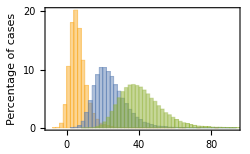

```mathematica
Histogram[{datd[[;;,2]]-datd[[;;,1]],dati3[[;;,2]]-dati3[[;;,1]],dati6[[;;,2]]-dati6[[;;,1]]},50,Frame->True,FrameStyle->Directive[Black,FontSize->10],FrameTicks->{{{{0,"0"},{5000,"5"},{10000,"10"},{15000,"15"},{20000,"20"}},Automatic},{Automatic,Automatic}},FrameLabel->{"Days between symptom onset","Percentage of cases"},ImageSize->250]
```

```mathematica
The short period of time between generations and broad variance of the time between symptoms given transmission from A to B means that it takes a large number of intermediate transmissions before events regularly become inconsitent with direct transmission
```

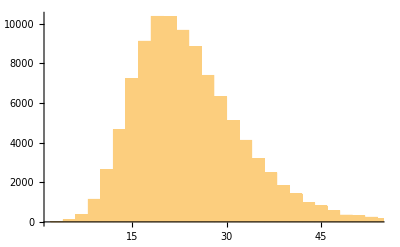

```mathematica
Histogram[dati3[[;;,2]]-dati3[[;;,1]]]
```

```mathematica
Output from analysis
```

```mathematica
SetDirectory["/Users/Chris/Documents/Coronavirus/HE_Distributions/PairwiseCode/A2BCore"];
b=Flatten[Import["Indirect_borderline_loc.out","Table"]];
u=Flatten[Import["Indirect_unlikely_loc.out","Table"]];
```

```mathematica
dat=Table[{100000-b[[i]]-u[[i]],b[[i]],u[[i]]},{i,1,Length[u]}]
```

{{82051,13548,4401},{48101,31154,20745},{26499,35277,38224},{16101,29502,54397},{5198,19326,75476},{1185,8961,89854},{266,3278,96456},{37,910,99053}}

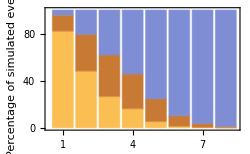

```mathematica
BarChart[dat,ChartLayout->"Stacked",Frame->True,FrameTicks->{{{{0,"0"},{20000,"20"},{40000,"40"},{60000,"60"},{80000,"80"},{100000,"100"}},Automatic},{{1,2,3,4,5,6,7,8},Automatic}},FrameStyle->Directive[Black,FontSize->10],FrameLabel->{"Number of intermediate transmissions","Percentage of simulated events"},ImageSize->250]
```

```mathematica
dat=Flatten[Import["Direct_loc.out","Table"]];
BarChart[dat,ChartLayout->"Stacked",Frame->True,FrameTicks->{{{{0,"0"},{20000,"20"},{40000,"40"},{60000,"60"},{80000,"80"},{100000,"100"}},Automatic},{Automatic,Automatic}},FrameStyle->Directive[Black,FontSize->10],FrameLabel->{"Direct","Percentage of simulated events"},ImageSize->87.5,PlotRange->{{0.3,1.7},All},AspectRatio->3]
```

-Graphics-

```mathematica
dat
```

{95001,4077,922}

```mathematica
?BarChart
```

```mathematica
90*6.0325/6.2089
```

87.443

```mathematica
l=-4;
N[Log[Exp[l]/4]]
```

-5.38629